```mathematica
msolv[n_]:=Reduce[1/a+1/b==1/n&&a>0&&b>=a,{a,b},Integers]
nsolns[n_]:=Length[msolv[n]]
Map[nsolns,Range[2,20]]

fsoln[n_]:=Total[Map[#[[2]]&,FactorInteger[n]]]

nsolns[9 7 5 3^2 2^4]
11 9 7 5 3^2 2^2
```

{2,2,3,2,5,2,4,3,5,2,8,2,5,5,5,2,8,2,8}

365

124740

```mathematica
{a,b}->{a==3&&b==4}
```

{a,b}→{a==3&&b==4}

```mathematica
13*12
```

156

Mod::indet: Indeterminate expression Mod[4096, 0] encountered.

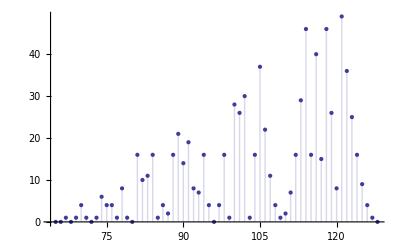

```mathematica
DiscretePlot[Mod[64 a,a-64],{a,64,128}]
```

```mathematica
nsolns[2 3 5 7 11 13 17]
2 3 5 7 11 13 17
nsolns[2^3 3^3 5^4 7]
```

1094

510510

662

```mathematica
(* 5 unique prime factors *)
nsolns[2]
nsolns[2^2]
nsolns[2 3]
nsolns[2^2 3]
nsolns[2 3 5]
nsolns[2^2 3^2]
nsolns[2 3 5 7 11 13]
nsolns[3 5 7 11 13 17]
nsolns[2^2 3 5 7 11 13]
nsolns[2 3^2 5 7 11 13]
nsolns[2 3^2 5 7 11 13 17]
```

2

3

5

8

14

13

365

365

608

608

1823

```mathematica
msolv[2]
```

(a==3&&b==6)||(a==4&&b==4)

```mathematica
N[Log[2,2 3^2 5 7 11 13 17]]
```

20.5465

```mathematica
Simplify[Solve[1/141+b==1/120,b]]
```

{{b→7/5640}}

```mathematica
Select[Range[120,240],Not[PrimeQ[#]]&]
{2,4,8,3,5}
```

{120,121,122,123,124,125,126,128,129,130,132,133,134,135,136,138,140,141,142,143,144,145,146,147,148,150,152,153,154,155,156,158,159,160,161,162,164,165,166,168,169,170,171,172,174,175,176,177,178,180,182,183,184,185,186,187,188,189,190,192,194,195,196,198,200,201,202,203,204,205,206,207,208,209,210,212,213,214,215,216,217,218,219,220,221,222,224,225,226,228,230,231,232,234,235,236,237,238,240}

{2,4,8,3,5}

```mathematica
FactorInteger[1260]
```

{{2,2},{3,2},{5,1},{7,1}}

```mathematica
FactorInteger[1680]
```

{{2,4},{3,1},{5,1},{7,1}}

```mathematica
FactorInteger[2310]
nsolns[2310]
```

{{2,1},{3,1},{5,1},{7,1},{11,1}}

122

```mathematica
Solve[1/a+1/b==1/n,b]
```

{{b→(a n)/(a-n)}}

```mathematica
nsolns[2 3]
nsolns[2 5]
nsolns[2 7]
nsolns[2 5 7]
nsolns[2 5 11]
```

5

5

5

14

14

```mathematica
FactorInteger[55440]
```

{{2,4},{3,2},{5,1},{7,1},{11,1}}

```mathematica
PrimeQ[101]
```

True

```mathematica
nsolns[2^5 3^3 5^1 7 11]
2^4 3 5 7 11 13
```

1040

240240

166320

332640

```mathematica
Select[Range[1,100],PrimeQ]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}